```mathematica
(*Module[{phi, x, y},
phi[x_, y_]:=a0(x^2-a^2)(y^2-b^2);
f[x_, y_]:=D[phi[x, y], x]^2+D[phi[x, y], y]^2-2 nu ro phi[x, y];
inita0=Solve[D[Integrate[f[x, y], {x, -a, a}, {y, -b, b}], a0]==0, a0];
Print[inita0];
Print[phi[0, 0]/.inita0[[1]]/.a->1/.b->1//N]
];*)
```

```mathematica
(*Module[{phi, x, int, y},
phi[x_, y_]:=(a0+a2(x^2+y^2))(x^2-a^2)(y^2-a^2);
f[x_, y_]:=D[phi[x, y], x]^2+D[phi[x, y], y]^2-2 nu ro phi[x, y];
int=Integrate[f[x, y], {x, -a, a}, {y, -b, b}];
inita2=Solve[D[int, a0]==0 && D[int, a2]==0, {a0, a2}];
Print[inita2];
Print[phi[0, 0]/.inita2[[1, 1]]/.inita2[[1, 2]] /.a->1 /.b->1 //N]
];*)
```

{{a0→(5 nu ro)/(a^2+b^2)}}

0.15625 nu ro

-Graphics3D-

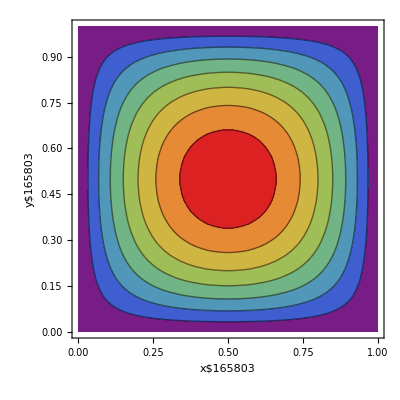

```mathematica
Module[{phi, x, y},
phi[x_, y_]:=a0(x-a)x y(y-b);
f[x_, y_]:=1/2 D[phi[x, y], x]^2+1/2 D[phi[x, y], y]^2-2 nu ro phi[x, y];
a0Ans=Solve[D[Integrate[f[x, y], {x, 0,a}, {y, 0, b}], a0]==0, a0];
Print[a0Ans];
Print[phi[a/2, b/2]/.a0Ans[[1]]/.a->1 /.b->1//N];
Print[Plot3D[{phi[x, y]/.a0Ans[[1]]/.a->1/.b->1/.nu->1/.ro->1}, {x, 0, 1}, {y, 0, 1},PlotRange -> All, AxesLabel -> Automatic, 
           ImagePadding -> 20, Mesh -> 35, 
           ColorFunction -> "Rainbow", Boxed -> False]]
Print[ContourPlot[{phi[x, y]/.a0Ans[[1]]/.a->1/.b->1/.nu->1/.ro->1}, {x, 0, 1}, {y, 0, 1},PlotRange -> All, AxesLabel -> Automatic, 
           ImagePadding -> 20, Mesh -> 35, 
           ColorFunction -> "Rainbow"]]
];
```

```mathematica
Module[{phi, x, int, y},
phi[x_, y_]:=(a0+a1(x+y)+a2(x^2+y^2))(x-a)x y (y-b);
f[x_, y_]:=1/2 D[phi[x, y], x]^2+1/2 D[phi[x, y], y]^2-2 nu ro phi[x, y];
int=Integrate[f[x, y], {x, 0, a}, {y, 0,b}];
a2Ans=Solve[D[int, a0]==0 &&D[int, a1]==0&& D[int, a2]==0, {a0,a1,  a2}];
Print[a2Ans];
Print[phi[a/2, b/2]/.a2Ans[[1, 1]]/.a2Ans[[1, 2]]/.a2Ans[[1, 3]]/.a->1 /.b->1//N]
];
```

{{a0→(35 (50 a^10 nu ro+75 a^9 b nu ro+1815 a^8 b^2 nu ro-2520 a^7 b^3 nu ro+10199 a^6 b^4 nu ro-13830 a^5 b^5 nu ro+10199 a^4 b^6 nu ro-2520 a^3 b^7 nu ro+1815 a^2 b^8 nu ro+75 a b^9 nu ro+50 b^10 nu ro))/(125 a^12+13475 a^10 b^2-22050 a^9 b^3+85355 a^8 b^4-119910 a^7 b^5+143626 a^6 b^6-119910 a^5 b^7+85355 a^4 b^8-22050 a^3 b^9+13475 a^2 b^10+125 b^12),a1→-((1050 (a+b) (5 a^8 nu ro-5 a^7 b nu ro+26 a^6 b^2 nu ro-5 a^5 b^3 nu ro+10 a^4 b^4 nu ro-5 a^3 b^5 nu ro+26 a^2 b^6 nu ro-5 a b^7 nu ro+5 b^8 nu ro))/(125 a^12+13475 a^10 b^2-22050 a^9 b^3+85355 a^8 b^4-119910 a^7 b^5+143626 a^6 b^6-119910 a^5 b^7+85355 a^4 b^8-22050 a^3 b^9+13475 a^2 b^10+125 b^12)),a2→(1050 (5 a^8 nu ro+42 a^6 b^2 nu ro+10 a^4 b^4 nu ro+42 a^2 b^6 nu ro+5 b^8 nu ro))/(125 a^12+13475 a^10 b^2-22050 a^9 b^3+85355 a^8 b^4-119910 a^7 b^5+143626 a^6 b^6-119910 a^5 b^7+85355 a^4 b^8-22050 a^3 b^9+13475 a^2 b^10+125 b^12)}}

0.146097 nu ro